```mathematica
(*En<0*)
schrodinger1[V_,En_]:=(-hbar^2/(2m) Laplacian[#,{x}]+(V-En)#)&;
```

```mathematica
(*left*)
eq1=0==schrodinger1[0,En][psi1[x]]//ExpandAll
```

0==-En psi1[x]-(hbar^2 psi1''[x])/(2 m)

```mathematica
DSolve[eq1,psi1[x],x]
```

{{psi1[x]→C[1] Cos[(√2 √En √m x)/hbar]+C[2] Sin[(√2 √En √m x)/hbar]}}

```mathematica
betarule={En->-hbar^2 beta^2/(2m)}
```

{En→-(beta^2 hbar^2)/(2 m)}

```mathematica
dsol1=DSolve[eq1,psi1[x],x][[1]]/.betarule//PowerExpand
```

{psi1[x]→C[1] Cosh[beta x]+ⅈ C[2] Sinh[beta x]}

```mathematica
psi1[x_]:=b E^(beta x)
```

```mathematica
(*middle*)
```

```mathematica
eq2=0==schrodinger1[-V0,En][psi2[x]]//ExpandAll
```

0==-En psi2[x]-V0 psi2[x]-(hbar^2 psi2''[x])/(2 m)

```mathematica
DSolve[eq2,psi2[x],x]
```

{{psi2[x]→ⅇ^((√2 √(-En m-m V0) x)/hbar) C[1]+ⅇ^(-(√2 √(-En m-m V0) x)/hbar) C[2]}}

```mathematica
krule={En->-V0+hbar^2 k^2/(2m)};
```

```mathematica
dsol2=DSolve[eq2,psi2[x],x][[1]]/.krule//PowerExpand//FullSimplify[#,{hbar>0,En<0,k>0}]&
```

{psi2[x]→ⅇ^(-ⅈ k x) (ⅇ^(2 ⅈ k x) C[1]+C[2])}

```mathematica
psi2[x_]:=c E^(I k x)+d E^(I k x)
```

```mathematica
(*right*)
```

```mathematica
psi3[x_]:=a E^(beta x)
```

```mathematica
(*even parity*)
```

```mathematica
psi1[x_]:=a E^(beta x)
psi2[x_]:=Cos[k x]
psi3[x_]:=a E^(-beta x)
bound={psi1[-a]==psi2[-a],psi1'[-a]==psi2'[-a]}
```

{a ⅇ^(-a beta)==Cos[a k],a beta ⅇ^(-a beta)==k Sin[a k]}

Notice that k^2 + beta^2=2 mV0/hbar^2, let a=1, 2 mV0/hbar^2=5, make the plot

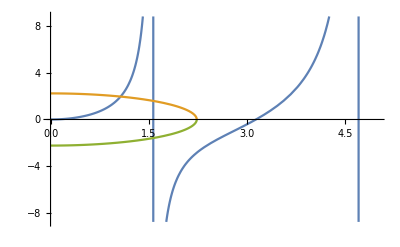

```mathematica
Plot[{k Tan[k],Sqrt[5-k^2],-Sqrt[5-k^2]},{k,0,5}]
```

```mathematica
ans1=FindRoot[k Tan[k]==Sqrt[5-k^2],{k,1}]
```

{k→1.07121}

```mathematica
ans2={beta->Sqrt[5-k^2]}/.ans1
```

{beta→1.96278}

```mathematica
ans3={a->E^beta Cos[k]}/.ans2/.ans1
```

{a→3.41048}

```mathematica
psi1[x_]=a E^(beta x)/.ans3/.ans2
```

3.41048 ⅇ^(1.96278 x)

```mathematica
psi2[x_]:=Cos[k x]/.ans1
```

```mathematica
psi2[x]
```

Cos[1.07121 x]

```mathematica
psi3[x_]:=3.4104753511793993 ⅇ^(-1.962779820909503 x)
```

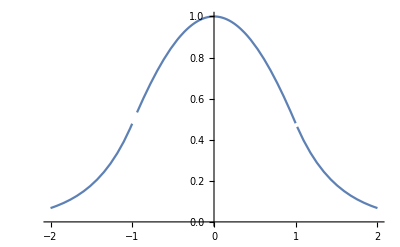

```mathematica
Plot[Piecewise[{{psi1[x],x<-1},{psi2[x],-1<x<1},{psi3[x],x>1}}],{x,-2,2}]
```

```mathematica
(*odd parity*)
```

```mathematica
psi1[x_]:=a E^(beta x)
psi2[x_]:=Sin[k x]
psi3[x_]:=-a E^(-beta x)
bound={psi1[-a]==psi2[-a],psi1'[-a]==psi2'[-a]}
```

{a ⅇ^(-a beta)==-Sin[a k],a beta ⅇ^(-a beta)==k Cos[a k]}

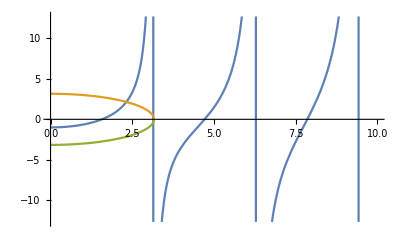

```mathematica
Plot[{-k Cot[k],Sqrt[10-k^2],-Sqrt[10-k^2]},{k,0,10}]
```

```mathematica
ans1=FindRoot[-k Cot[k]==Sqrt[10-k^2],{k,2}]
```

{k→2.31858}

```mathematica
ans2={beta->Sqrt[10-k^2]}/.ans1
```

{beta→2.15039}

```mathematica
ans3={a->E^beta Cos[k]}/.ans1/.ans2
```

{a→-5.84013}

```mathematica
psi1[x_]:=a E^(beta x)/.ans3/.ans2
```

```mathematica
psi1[x]
```

-5.84013 ⅇ^(2.15039 x)

```mathematica
psi2[x_]:=Sin[k x]/.ans1
```

```mathematica
psi2[x]
```

Sin[2.31858 x]

```mathematica
psi3[x_]:=-a E^(-beta x)/.ans3/.ans2
```

```mathematica
psi3[x]
```

5.84013 ⅇ^(-2.15039 x)

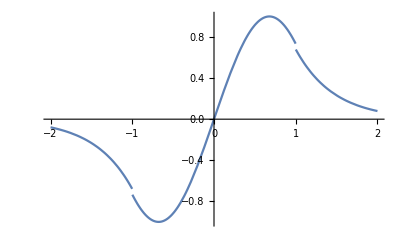

```mathematica
Plot[Piecewise[{{psi1[x],x<-1},{psi2[x],-1<x<1},{psi3[x],x>1}}],{x,-2,2}]
```